# Introduction To Differentiable Manifolds

Brian Beckman
Dec 2023

“I can’t understand anything in general unless I’m carrying along in my mind a specific example and watching it go. Some people [think] I’m following the steps mathematically, but that’s not what I’m doing.” 

	— R. P. Feynman

## Abstract

This tutorial offers a bridge between the abstract mathematics of differentiable manifolds and computational practice. Computational practice means writing software in terms of matrices and vectors containing real and complex numbers. We offer elementary examples fully explained and illustrated at length.

Nowadays, some understanding of differential geometry and topology is increasingly necessary even if your only objective is to do calculations, not to do proofs. That’s because differential geometry and topology have crept from mathematics and physics into engineering. In simulation, robotics, and computer games, they support much better numerical performance than do older approaches.[19][20] Philosophically, it seems that differentiable manifolds, in 3, 4, 8, and more dimensions, rule all the natural World, all the way from quarks through robots to black holes and superclusters of galaxies. Differential geometry offers one set of tools for all these domains in place of many sets of incompatible tools, one for each domain.

Contemporary books and papers on applications of differential geometry and topology can be challenging. Many are written in highly abstract mathematical style (definitions and proofs without examples), with more generality than needed for applications (unphysical topologies), and with unfamiliar notation. If you didn’t learn fiber bundles, exterior calculus, and Lie theory in school and you want to catch up fast, this tutorial might be interesting to you. You’ll be equipped to read papers without choking on things you’ve never heard of, to get through to the juicy bits where we learn from the heavy math how to do calculations.

Looking forward, I have some notebooks in the works on integrating equations of motion of mechanical systems on Lie groups. The Lie groups needed for simulation and control are differentiable manifolds, abstract curved spaces analyzed through differential geometry and topology.

## Prerequisites

We assume linear algebra and multivariable calculus: typical undergraduate applied mathematics for engineering and science. We do not assume topology, point-set topology, real analysis, tensors, exterior algebra and calculus, differential forms, generalized Stokes’ theorem, Lie groups, Lie algebras, or Hodge theory. We do not even assume basic concepts of pure mathematics, like equivalence class, set theory, bijection, surjection, and partial function.

The following terms should immediately bring to mind a concrete realization and a calculational procedure, i.e., we assume you know how to write software with them: matrix, inverse, transpose, determinant, column vector, row vector, divergence, gradient, curl, Jacobian, Hessian. We also assume you know that column and row vectors are punned as flat lists in Mathematica.

## References

I recently discovered Reference 21. I recommend it highly, and by a special method: read Act V first, then work backwards. You’ll taste the exterior calculus, a grand simplification of algebraic machinery, and have it in mind while you recapitulate the geometry itself in Acts I through IV.

I first learned the topics of this tutorial from Reference 17. It is also great, but the algebraic machinery can get overwhelming. I especially appreciate References 15 and 21 by reflecting on 17, wishing I had had 15 and 21 back in my youth. I do not regret taking the hard road, but I’m not sure it’s best for everyone.

I recently discovered Reference 22. I recommend it for checking hand calculations, but not for supplanting them. There seems to be no substitute for drawing and writing mathematics by hand with physical paper and pencils and pens, but Mathematica is indispensable for making sure you got it right.

The rest of the references are helpful for applications, especially for simulation and control. We’ll focus on some of them in future tutorials.

Jack B Kuipers, Quaternions and Rotation Sequences, Princeton University Press, 1999.

Jeongseok Lee, Karen Liu, Frank C. Park, Siddhartha S. Srinivasa, A Linear-Time Variational Integrator for Multibody Systems, 2018, https://arxiv.org/abs/1609.02898

Ari Stern, Discrete Geometric Mechanics and Variational Integrators, 2006, http://ddg.cs.columbia.edu/SIGGRAPH06/stern-siggraph-talk.pdf.

Ethan Eade, Lie Groups for 2D and 3D Transformations, 2017, http://ethaneade.com/lie.pdf.

NIST: Digital Library of Mathematical Functions, https://dlmf.nist.gov.

Brian C. Hall, Lie Groups, Lie Algebras, and Representations, Second Edition, 2015, Springer.

Guangyu Liu, Modeling, stabilizing control and trajectory tracking of a spherical inverted pendulum, PhD thesis, 2007, University of Melbourne, 
https://minerva-access.unimelb.edu.au/handle/11343/37225.

Wikipedia, Tennis-Racket Theorem, https://en.wikipedia.org/wiki/Tennis_racket_theorem.

Marin Kobilarov, Keenan Crane, Mathieu Desbrun, Lie Group Integrators for Animation and Control of Vehicles, 2009 (https://www.cs.cmu.edu/~kmcrane/Projects/LieGroupIntegrators/paper.pdf).

Ari Stern, Mathieu Desbrun, Discrete Geometric Mechanics for Variational Time Integrators, 2006 (http://www.geometry.caltech.edu/pubs/SD06.pdf).

Kenth Engø, On The BCH Formula in 𝔰𝔬(3), https://www.researchgate.net/profile/Kenth_Engo-Monsen2/publication/233591614_On _the _BCH-formula_in _so3/links/004635199177f69467000000/On-the-BCH-formula-in-so3.pdf.

Alexander Van-Brunt, Max Visser, Explicit Baker-Campbell-Hausdorff formulae for some specific Lie algebras, https://arxiv.org/pdf/1505.04505.pdf.

Wikipedia, Baker-Campbell-Hausdorff Formula, https://en.wikipedia.org/wiki/Baker% E2 %80 %93 Campbell % E2 %80 %93 Hausdorff_formula.

Jerrold E. Marsden, Tudor S. Ratiu, Introduction to Mechanics and Symmetry, Second Edition, 2002.

John H. Hubbard and Barbara Burke Hubbard, Vector Calculus, Linear Algebra, and Differential Forms: A Unified Approach, 5th edition, http://matrixeditions.com/5thUnifiedApproach.html, 2015.

Paul R. Halmos, Naive Set Theory, 2015.

David Lovelock and Hanno Rund, Tensors, Differential Forms, and Variational Principles, 1975.

Ralph Abraham and Jerrold E. Marsden, Foundations of Mechanics: 2nd Edition, 1980.

Taeyoung Lee, Melvin Leok, and N. Harris McClamroch, Discrete Control Systems, (https://arxiv.org/abs/0705.3868)

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Global Formulations of Lagrangian and Hamiltonian Mechanics on Manifolds, Springer (https://a.co/d/0lTbL9t)

Tristan Needham, Visual Differential Geometry and Forms, https://a.co/d/9hoKekz.

xAct, Efficient tensor computer algebra for the Wolfram Language, http://xact.es/index.html.

Blanco, Jose-Luis, A tutorial on SE(3) transformation parameterizations and on-manifold optimization, Technical Report #012010, Universidad de Malaga (https://jinyongjeong.github.io/Download/SE3/jlblanco2010geometry3d_techrep.pdf).

## Cheat Sheet

The following table summarizes chapter 4 of Reference [14]. To keep it small, it is not self-contained, but rather presented in very roughly the order of this tutorial to help you jump to various parts, also as a reference to return to. Many items might not be understandable without forward reading. Reference [14] is authoritative for details and in the case of errors in the table and in the rest of this document. The red highlighted item is a particularly obtuse bit of notation, and we explain it at length in the body of the tutorial.

NOTION | NOTATION | DEFINITION | REMARKS
Manifold | M, N | abstract collection
of abstract points | add differentiable
structure
 Coordinate Chart | (U,φ) | U⊂M , U open
φ:U↔φ (U)⊂ℝ^n | φ(m)=
{x^1,x^2,…,x^n}
Open Set | U, U' | primitive from 
topology | detailed
knowledge not
needed
Compatible Charts | (U,φ),(U^′,φ') | φ'◦ φ^-1|φ (U∩U') 
is C^∞; φ (U∩U')and
φ'(U∩U')are open |  
Differentiable Manifold | Every m∈M is in 
at least one chart | M is a union of
compatible charts |  
Differentiable Structure | Maximal atlas |   |  Collection of all 
compatible charts
Neighborhood | φ^-1 applied to
neighborhood in ℝ^n | Hausdorff topology:
m≠m'⇒
∃non-intersecting
neighborhoods in M |  
Equivalent curves | c_1(0)=c_2(0)
(φ ◦ c_1)'(0)=(φ ◦ c_2)'(0) | c_1:ℝ→M
c_2:ℝ→M | for some chart φ
Tangent Vector | v(m) | Equivalence class
of curves |  
Equivalence Class | [c(t)] | All curves with same
value and derivatives
through some chart
 φ at t=0 |  
Tangent elsewhere
on a curve | ∀ c(t), def c'(s)at c(s)
dc/dt|_(t=0) | c'(s)∈eqv. class
[(t↦c(s+t))|_(t=0)] | finite distance 
s down curvec(t)
Tangent Space | T_m M | Space of all tangent 
vectors at m∈M | THEOREM: T_m M 
is a vector space
Components of a 
Vector | v^i=d/dt(φ ◦ c)^i|_(t=0) | Superscript runs
over the dimensions |  Each component
is a real number
Tangent Bundle | TM=⊔(T_m M)_(m ∈ M) | Includes local
coordinates and 
components of 
vectors | dimension is2n;
 ⊔ is disjoint union
Natural Projection | τ_M:TM→M
τ_M^-1(m)=T_m M | Returns attachment
point of a vector | τ_M^-1(m) is the fiber
of TM at m

Differentiable,
Derivative | With f:M→N
T_m f:T_m M→T_(f(m))N | T_m f is a linear map
i.e., a matrix, s.t.
T_m f·v=
T_m f·dc/dt|_(t=0)=
d/dt f(c(t))|_(t=0) |  M and N are
manifolds
Diffeomorphism | f:M<->N | Bijective,
differentiable,
& diff'ble inverse | donut &
coffee cup are
diffeomorphic

## Motivating Example

### Get Your Kicks on Route 55

Let M, a manifold, be a set of abstract points representing a part of the surface of the Earth between St. Louis in the North and New Orleans in the South, and wide enough for the Mississippi River. We call it a manifold because it’s many-folded, that is, curved. Though this one doesn’t have many folds, more general cases do.

This manifold, however, is sufficiently curved to be interesting and illustrative. To start, M is just a set of points on the globe. There is obvious organization of the points. It is obvious to say that "Memphis is between St. Louis and New Orleans" and "Interstate 55 roughly follows The River." But we don't yet know how to be precise in those statements because of the curvature. We know Euclidean geometry, Cartesian analytical geometry, and trigonometry we learned in school, and we know they don’t work on curved surfaces. We can’t calculate the distance from St. Louis to New Orleans simply by subtracting their latitude-longitude coordinates. The math we know only works on flat surfaces. Can we relate the math we know to this globe? That’s the topic of differentiable manifolds in a nutshell: relating sets of points on curved manifolds to flat, Euclidean hyperplanes where we know how to calculate. Sometimes, the curved manifolds like the globe have two dimensions. Sometimes, they have many more. The SU(3) group of quantum chromodynamics is a manifold of eight real dimensions (https://en.wikipedia.org/wiki/Special_unitary_group).

-Graphics-

### Definition: Parameterized Curve

Imagine a collection of parameterized curves that map real numbers (parameters) to points in the manifold, the globe in our example. Denote one member of that collection as c. c is a function. The value of that function, c(t), given a real number t, is a point m∈M in the manifold. As t, a real number, advances, c(t) names one point on the Earth’s surface, then another point nearby, then another even further, and so on.

How do we “name” points in the manifold and how we decide what “nearby” means? Don’t say “latitude and longitude!” just yet, because that’s a particular numerical scheme, a chart, and we’re not there yet. There are lots of other ways to name points on the Earth’s surface.

### Definition: Point

What’s a point? It’s smaller than a ten-foot square. It’s smaller than an inch. It’s smaller than an atom. It’s smaller than an atomic nucleus.

Physics hints that we can’t measure anything smaller than the Planck length, about 10^-33 cm, so that will do. That’s really small, by the way: a hundred million trillion (10^20) times smaller than an atomic nucleus, which is about 10^-13 cm across. If we can uniquely name any little Planck square, 10^-33 cm on a side, anywhere on the globe, could anyone ask for anything more in the real world?

Mathematicians, of course, reason outside the real world with uncountable infinities of infinitesimally small points. Such reasoning is necessary for a rigorously logical understanding of calculus, but we don't go that far. We're trying to stay concrete. See ref [15] for a beautiful account of calculus from a rigorously logical point of view. The abstract notation we’re explaining in this tutorial assumes you have heard of that point of view, which is artificially and ironically called real analysis, based on point-set topology. You don’t have to be proficient in those topics to do calculations.

### What3Words: Unique Names for Ten-Foot Squares

The web site "What3Words.com" gives a unique name to every ten-foot square on the surface of the Earth (it might not work very close to the North and South Poles).

Pick some point on the surface. We showed above that, for practical purposes, a point is a Planck square. Pick a specific Planck-square in a specific nucleus of a specific atom in a specific USGS geodetic marker in Winona, Mississippi, the seat of Montgomery County. "What3Words" has a unique name for the ten-foot square that encloses our point. That name is "jokers.priced.pursuit" (https://map.what3words.com/jokers.priced.pursuit).

We'll give the same name to our Planck-square: "jokers.priced.pursuit," or m_W for short. Yes, we’re using the same name for a single Planck square as for a ten-foot-square patch that contains 10^71 other Planck squares.

-Graphics-

The important point is that these three-word string-names contain no metrical information. Given two string-names, it’s impossible to tell whether the corresponding ten-foot squares are adjacent or ten thousand miles apart. From a user’s point of view, the names are randomly chosen.

### What21Words: Unique Names for Planck Squares

It turns out that a string of twenty-one words from a personal vocabulary of mine suffices to uniquely name every one of about 56×10^83 Planck squares that could tile the Earth, with a practical algorithm that we could code up easily. Practically speaking, we could name points on the Earth to any level of refinement or detail we want. We are not stuck with ten-foot precision.

### Definition: Manifold

To a mathematician, a manifold is an uncountably infinite set, with elaborate structure and rules, of abstract points of size exactly zero (in the limit). The purpose of the structure and rules is to make linear algebra and ordinary calculus work so that any of us can do calculations on abstract and nearly arbitrarily curved spaces! Calculus, however, works in Euclidean, n-dimensional vector spaces, ℝ^n. The structure and rules of manifolds let us set up Euclidean spaces almost anywhere on a manifold.

### Aside: Do-It-Yourself Naming

If you are not interested in how to name points and squares with strings of words, nor in my guesses about how “What3Words” works, skip this section.

It’s interesting to figure out how “What3Words” might work. This is my guess.

There are a little fewer than 56×10^12 ten-foot squares on Earth. The surface area of Earth is 4π r_⊕^2≈197 million square miles, where r_⊕ is the radius of Earth, about 3959 miles. Call it 200 million square miles to get an overestimate.

```mathematica
UnitConvert[Entity["Planet","Earth"][EntityProperty["Planet","SurfaceArea"]], "Miles"^2]
```

1.9694×10^8 mi^2

Each square mile is 5280^2=27878400 square feet, call it 28 million. That makes 5600 trillion (million million) square feet for the whole Earth, or about 5.6×10^15.

```mathematica
UnitConvert[Entity["Planet","Earth"][EntityProperty["Planet","SurfaceArea"]], "Feet"^2]
```

5.4903×10^15 ft^2

Each 10-foot square comprises 100 square feet, so divide 5600 trillion for a total of about 56×10^12, 56 trillion squares.

#### 56 × 10^12 Unique Names

If we’re going to give 56×10^12 squares each a unique name of three words, what size of vocabulary will we need? About (56×10^12)^(1/3)≈38258. That’s about twice the average adult’s vocabulary, according to The Economist (https://www.economist.com/johnson/2013/05/29/lexical-facts). Science magazine reckons that the average adult native speaker of English has a vocabulary of 42000 words counting “lemmas” like “help,” “helpful,” “helpfulness,” and words that are easy to understand by guessing, like “biblioklept” (https://www.sciencemag.org/news/2016/08/average-20-year-old-american-knows-42000-words-depending-how-you-count-them). By either reckoning, the vocabulary of 38258 words necessary for “What3Words” is entirely reasonable.

#### What4Words: Using My Own Dictionary

I can make my own version of “What3Words,” not an exact clone, because I don’t have their dictionary, but I do have my own 15141 words that I collected for word games:

To get 56 trillion unique combinations, I need four of my words (15141^4≈5.25555×10^16 is 900 times more than enough, but 15141^3≈3.47107×10^12 isn't enough). So my imaginary version of their web site would have to be “What4Words.”

#### Names for Planck Squares

We want to uniquely name every Planck square on Earth. How many of my words would we need?

A Planck length is 10^-33 cm, and a Planck square is 10^-66 cm^2, or

```mathematica
UnitConvert[Quantity[1.0*10^-66,"square cm"],"square ft"]
```

1.07639×10^-69 ft^2

That means there are about 10^69 Planck squares per square foot, or about 5600×10^(12 + 69)=56×10^83 Planck squares on the surface of the Earth. The logarithm, base 15141, of (56×10^83) is about 20.27. I need at least that many of my words to uniquely identify every Planck square on Earth. A string of twenty-one of my words would be more than enough. Anyone, with a little effort, could even memorize a few of these strings of twenty-one words.

We have a practical scheme for naming every Planck square on Earth: every point that is a hundred million trillion times smaller than an atomic nucleus named with just twenty-one words in a string.

It's not crazy to imagine a "What21Words" web site for uniquely naming every Planck square on Earth. It is crazy to imagine a random assignment of names, because such would require a database with 56×10^83 rows, a lot more rows than there are electrons in the entire Universe (about 10^80, https://io9.gizmodo.com/5876966/what-if-every-electron-in-the-universe-was-all-the-same-exact-particle). However, we could implement “What21Words” by systematically numbering the Planck squares, tiling the Earth in strips of constant latitude or an ascending spiral, or with clever Twarock-Konestova or Caspar-Klug (soccer-ball) tilings (https://archive.bridgesmathart.org/2018/bridges2018-237.pdf), and then treating my words as numerals in radix 15141. We could even implement that right here and now in this notebook, but maybe you'd like to do that on your own, just for fun, of course.

It would not be secure. A dedicated hacker could discover our systematic scheme and then clone our site. How “What3Words" protects their intellectual property is anyone's guess, but if I were they, I might just use a random distribution and a database. It's just barely practical to have a database of 56 trillion items (e.g., InnoDB can do it). Lots of interesting crypto tricks like zero-knowledge proofs are conceivable, too, but let’s get back on track with manifolds.

### Curves near m_W

We’re using the same name for the ten-foot square from “What3Words” and for our specific Planck square in our specific nucleus or our specific atom of our specific geodetic marker in Winona, MS, but we won’t get confused.

Consider a bunch of parameterized curves, c(t), that all go through m_W. Adjust their parameters so that when t=0, all the curves go through m_W. The following picture illustrates three such curves.

-Graphics-

All these curves must always be, for any t∈ℝ whatever, in the manifold. That means they cannot wander off up into the sky or below the ground. We can’t go paragliding or mining with “What3Words.” But the curves can go in loops and whorls and knots, no problem.

### Differentiable

The curves can go in loops and whorls and knots, but they must must be at least long enough to straddle m_W when the parameter t of any curve is near zero, either side of zero. And the curves must be "differentiable" there, at t=0. What could that mean?

The usual definition for derivative, when applied to a curve c(t) at any t could only be to take two nearby points, c(t+h) and c(t), where h is small, subtract them, divide by h, and go to the limit, lim_(h→0) (c(t+h)-c(t))/h. That doesn't make sense because c(t+h)-c(t) can only mean "subtracting" two points in the manifold and we have no idea what subtraction could mean in the manifold. How do you subtract a point in St. Louis, say “hope.school.hype,”

-Graphics-

from a point in New Orleans, 600 miles away, say "joins.slides.predict?"

-Graphics-

Even if two points are really close, say the lamppost "bottle.ruled.varieties" in St. Louis

-Graphics-

and the next lamppost at "heavy.beyond.speeds,"

-Graphics-

we don't know how to "subtract" them. We can subtract angles or vectors, but not points.

### Definition: Chart

We need a chart, a way to convert points in the manifold to numerical things like angles or vectors. We’re only going to work with a trivial chart to keep this example simple and easy, but take a look at Wikipedia’s collection of map projections https://en.wikipedia.org/wiki/List_of_map_projections. Coming up with charts is difficult and is, in fact, a principal problem for mapmakers and manifold theorists. Many of these map projections were specially constructed in earlier times when people calculated distances, headings, and areas by hand or even in their heads. Various map projections are specialized for distances, angular headings, or areas, but can’t support all three, or even more than one, efficiently. A human navigator may need several charts to get the job done. Many charts are set up for physical measurements on flat paper with protractor, ruler, and compass. We still use those charts in computers, just with virtual protractors, rulers, and compasses.

### Distances: Coordinate and Metrical Distances

The web API (not necessarily the GUI) of “What3Words” implements a chart: you give it a three-word name and it gives you back a latitude and longitude. Latitudes and longitudes won’t yield distances directly by subtraction, but we can compute purely formal sums and differences, called coordinate distances. We’ll construct a slightly complicated function below that produces metrical distances from lats and lons — actual feet and miles on the ground that you’d get from an odometer. We won’t get into complicated charts like Wikipedia’s map projections. The purpose of this tutorial is to help you appreciate manifolds from simplified examples, not to get you into all the details.

### Definition: Open Sets (Trouble at the Poles)

Many charts of the Earth have trouble near the North and South Poles, but people don't ordinarily go to either place, so cartographers often park troublesome bits at the poles. “What3Words" goes way up in latitude, but I haven't found the North Pole, yet, because their display-maps don't show anything up there and I can't see what I’m doing. The South Pole seems to be at "greenhouses.recommitting.multiplexes" because the maps go crazy there and the web app doesn't behave well. We shouldn't play around where we know someone else's web app chokes up; that's a denial-of-service attack. So I gave up at the first sign of trouble, but there was trouble. Maybe it’s fixed, now.

In manifolds, we work with open sets, a purely formal, logical notion in topology. Open sets make calculus work by excluding troublesome bits. Our main goal, after all, is to make calculus work, so we mention open sets frequently in the statements and proofs of theorems. You don’t need to know topology to get through this tutorial, but you must resort to the formalities to strike out on your own.

Intuitions about open sets are notoriously misleading. Some sets can be both open and closed, and some sets can be neither open nor closed. It took 300 years to make calculus rigorously logical, after all, even though it was working well for physics and engineering from the days when Newton and Leibniz invented it. In fact, there is evidence that Archimedes, almost 2000 years prior, had the inklings of calculus (https://www.amazon.com/Archimedes-Codex-Revealing-Antiquitys-Scientist/dp/030681580X). See References [15] and [18] if you’re driven to know the topology behind calculus.

For applications in physics and engineering, the example of "trouble at the poles" is the intuition needed to understand an open set. You can go near a pole, and maybe inch a little nearer, and a littler nearer, but eventually you'll reach the limits of some practical computation and that will be the end of your session. You might as well have hit the excluded point dead-on.

### Definition: Dimension

Any chart on the Earth must let us convert three-word names or features like lampposts to pairs of numbers. We can't do with fewer than two numbers per point, and three wouldn't help. We’re near the Mississippi River and we’re not paragliding or mining. The Earth manifold represented by any chart is two-dimensional, exactly two-dimensional. Likewise, any chart of the Lie Group SU(3) must have exactly eight dimensions.

### Definition: Derivative of a Curve Through a Chart

We can’t compute derivatives of the curves, but we can compute derivatives of “well-behaved” charts composed with curves. Charts return pairs of real numbers, and we know how to compute derivatives of functions from one real parameter, t, to two real numbers, lat and lon. We speak of the derivative of a curve through a chart. What are the derivatives of one of our curves c(t) through the lat-lon chart φ? Write the derivatives as d(φ ◦ c)/dt, but that's still too abstract. We want our curve c(t) to go through m_W, ///jokers.priced.pursuit , when the parameter t=0.

The value of the chart at any point of the manifold is a tuple of numbers called the coordinates of the point in that chart. Charts are also called coordinate systems for this reason. It’s best to think of charts as functions, however, that convert abstract points on the manifold into tuples of real numbers. We then think of these tuples as members of ℝ^n, ordinary, flat, Euclidean space, where we know how to calculate. Incidentally, the whole machinery also works in the complex numbers, essential for quantum physics, but we’re not going there in this tutorial.

The web API of “What3Words” gives the coordinates of ///jokers.priced.pursuit as (lat=33.488883,lon=-89.731397). That’s not nearly the 34 or 35 decimal places we’d need for a Planck square, but let’s see how precise it is. One increment of latitude in the last place will be about 4.3 inches, not bad:

```mathematica
(rEarth=UnitConvert[Entity["Planet","Earth"][EntityProperty["Planet","Radius"]],"inch"])*(33.488884-33.488883)°
```

4.37776 in

At that latitude, one increment-in-last-place of longitude, using easy spherical trigonometry, is about

```mathematica
rEarth*Cos[33.488883°](-89.731397+89.731398)°
```

3.65102 in

### Definition: Function Composition

The symbol φ ◦ c is a function composition and means “a new function that feeds the output of one old function, the curve c, to the input of another old function, the chart φ.” Read the symbol φ ◦ c as “φ  [phi] compose c” or “ϕ on c.” We stress that the new composition φ ◦ c denotes one new function made up from two old functions, φ and c.

We could make our curve c return string-names from “What3Words" and then use their web API as our chart φ to look up lats and lons. That would be fun and even practical, but would only give us precision to ten feet. At least near m_W, we can get results good to about 5 inches. Going for higher precision comes at the cost of making our curve c return lats and lons and our chart φ do nothing, or, better stated, be the trivial chart.

All that talk about three-word names for nothing? No, because we could still do it that way, and we might have to do something like that in other applications. For the purposes of this example, to give you something easy to remember, a do-nothing chart φ and curves that “cheat” by giving lat-lons will be OK because we're only interested in the derivative of the composition φ ◦ c, namely d(φ ◦ c)/dt. If we were to use the string-form curve c, we'd have a lot more work to do with the chart, beating on the web API of “What3Words" to figure out how tiny increments in t lead to tiny increments in φ ◦ c. That wouldn’t be nice to beat on their web site. If they’re smart, they’ll notice we’re doing that and throttle our web access or even demand money! Let’s not.

### What Does “Nearby” Mean?

We know how to take two lat-lons and tell whether they’re nearby or not: look at the differences in the last place of their decimal expansions. Can we tell whether two points on the manifold are nearby? Not without a chart. This observation begs the question of “how do we construct a curve purely on the manifold, where nearby parameters t+h and t yield nearby points on the manifold?” We have to back into it from a chart. We’d have to construct something with sensible values for φ ◦ c(t), then apply the inverse chart function ϕ^-1 to get something on the manifold M.

### A First Curve

We need a curve c_1 to specify nearby points in the manifold for nearby values of t, where we understand "nearby" in the parameter to be increments in last place shown above. Let one increment of t correspond to 0.000001 degree — about five inches — in each of lat and lon for any t. To make sure that our c goes through m_W when t=0, write

ϕ ◦ c_1(t)=(33.488883+0.000001 t
-89.731397+0.000001t)

```mathematica
ϕc1$[t_]:={{33.488883+0.000001t},{-89.731397+0.000001t}};
```

That's our do-nothing chart composed with a particular c curve, a very boring curve that goes completely straight, but just one of uncountably many. The derivative of φ ◦ c_1 evaluated at t=0 is a constant (that’s what “completely straight” means):

(d(φ ◦ c_1))/dt|_(t=0)=(0.000001°
0.000001°)

```mathematica
D[ϕc1$[t],t]//MatrixForm
```

(1.×10^-6
1.×10^-6)

### A Second Curve

Imagine another curve c_2 that goes through m_W but wiggles in some way (through the chart) with lat and lon away from that point:

ϕ ◦ c_2(t)=(33.488883+0.000001 t+.000042(Sin[t]/t-1)
-89.731397+0.000001t*Cos[0.90t]^2)

```mathematica
ϕc2$[t_]:={{33.488883+0.000001 t+.000042(Sin[t]/t-1)},
{-89.731397+0.000001*t*Cos[0.90t]^2}};
```

That’s another curve through the chart. The composition ϕ ◦ c_2(t) has the same value and derivatives at m_w as does the composition ϕ ◦ c_1(t) with the boring, straight curve. The new curve c_2(t) is just another one of the uncountably many that have the same value and derivatives at m_W.

Here are plots, showing the wiggles, of the lat and lon parts of that new composition ϕ ◦ c_2(t) around t=0. Notice the very fine resolution of the vertical axes. The wiggles are small.

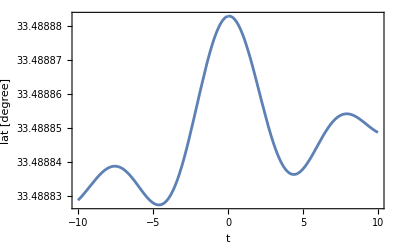

```mathematica
Plot[ϕc2$[t][[1]],{t,-10,10},Frame->True,FrameLabel->{{"lat [degree]",""},{"t","Latitude component of second curve composed with φ"}}]
```

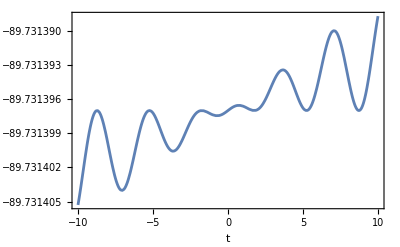

```mathematica
Plot[ϕc2$[t][[2]],{t,-10,10},Frame->True,FrameLabel->{{"lon [degree]",""},{"t","Longitude component of second curve composed with φ"}}]
```

Here they are together, making loops and whorls and knots. In this next plot, we can’t see the parameter t directly, but this is roughly what the curve looks like on the ground.

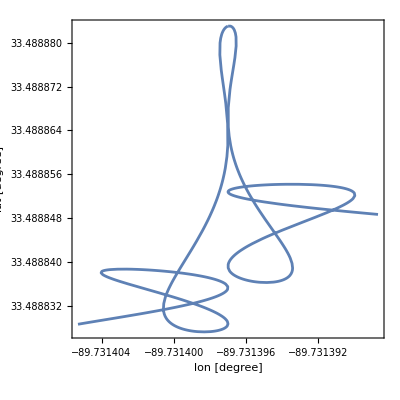

```mathematica
ParametricPlot[Reverse@ϕc2$[t],{t,-10,10},FrameLabel->{{"lat [degree]",""},{"lon [degree]","Second curve composed with φ, North UP"}},Frame->True,AspectRatio->1]
```

### Definition: Tangent Vector

Even though our two curves c_1 and c_2 behave very differently when t is not zero — one goes straight and the other one wiggles — they are indistinguishable, at least as to value and derivatives through the chart, when t=0. Here is the proof that the derivatives of ϕ ◦ c_2 are indistinguishable from the derivatives of ϕ ◦ c_1, which we know to be (0.000001°
0.000001°). We must take a limit to prevent division by zero:

```mathematica
D[ϕc2$[t],t]//FullSimplify//MatrixForm
```

(1.×10^-6+(0.000042 t Cos[t]-0.000042 Sin[t])/t^2
5.×10^-7+5.×10^-7 Cos[1.8 t]-9.×10^-7 t Sin[1.8 t])

```mathematica
Limit[D[ϕc2$[t],t],t->0]//MatrixForm
```

(1.×10^-6
1.×10^-6)

We begin by simply defining the words tangent vector to mean the set of all curves that are indistinguishable as to value and first derivatives through some chart at a certain point with parameter t=0. Don’t go crazy trying to think how a set of curves could be called a vector, when you know full well that a vector is a tuple of numbers or an arrow pointing from one point to another, not a set of curves! We could use words other than “tangent vector,” like blueberry blancmange, but we give some discussion to explain why the words tangent vector are sensible, very sensible.

The two curves we wrote are two elements of the tangent-vector-as-a-set. We can come up with many more. The number of equivalent curves is uncountable: just change the hard-coded numbers 0.00042 and 0.90 by small, real-number amounts to get new, different curves. The real numbers are uncountable. The values and derivatives of every curve in the same tangent-vector set as our two curves are the same m_W and the same (0.000001
0.000001) at t=0.

It makes sense to lump all the uncountably many curves with the same values and the same derivatives into one collection, and it makes a twisted kind of sense to call the collection THE tangent vector. Consider another collection of curves with the same value m_W as the first collection, but different derivatives through the chart, say (0.0000022
-0.0000015). We really can compute dot products between the derivatives of any curve in one tangent-vector set and the derivatives of any curve in another tangent-vector set rooted at the same m_W to get the cosine of an angle. We might need that angle for navigation. The angle happens to be

ArcCos[((0.000001
0.000001)ᵀ.(0.0000022
-0.0000015))/(Norm[(0.000001
0.000001)]Norm[(0.0000022
-0.0000015)])]=79.2869Degree

That angle is a metrical property that pertains only to that one point, and that's why it's called tangent: the two derivative sets inhabit the same flat 2-space, where all our school math like dot product works. But the flat 2-space is glued to exactly one point of the manifold. The curved surface of the manifold falls away from the tangent plane on all sides, making metrical calculations difficult. Dot products of 2-vectors only work in flat 2-spaces with the basic orthogonal coordinate system and when the vectors are rooted at the same point.

#### Aside: Only Direction Matters?

Rewrite Equation 4:

ArcCos[((0.000001
0.000001)/Norm[(0.000001
0.000001)])ᵀ.((0.0000022
-0.0000015)/Norm[(0.0000022
-0.0000015)])]=79.2868Degree

Notice that it’s the ArcCos of two normalized vectors. We might consider only normalized vectors if we were concerned only with dot products. In other words, we might be tempted to think of (0.000001
0.000001) and (0.000001
0.000001)/Norm[(0.000001
0.000001)] as equivalent. But doing so would not let us distinguish vectors by magnitude, and we want to do that.

#### Any Old Chart Will Do

We have a composition ϕ ◦ c that yields lat and lon for any curve c. Let’s plot a couple of vectors against a lat-lon coordinate grid. Then, let’s shear the grid and watch the coordinates of the vector tips change. In the plot, the coordinate numbers are relative to the vector base, a point in the manifold where the parameter t of the curve c(t) is 0. Emphasis: the vectors do not change: they are geometric entities attached to the manifold at c(0), independent of the coordinate grid, that is, independent of the chart. Only the coordinates of the vector tips change.

```mathematica
origin$={1,1};
v1Tipx$={ⅇ,√2}+origin$;
v2Tipx$={√3,π}+origin$;
v1$={Thick,Darker[Red],Arrow[{origin$,v1Tipx$}]};
v2$={Thick,Darker[Green],Arrow[{origin$,v2Tipx$}]};
originDot$=Disk[origin$,0.075];
textOffset$={0.35,0.15};
With[{ncells=5,xo=-1.2,yo=-0.45,xf=2,yf=1.025},
box$={White,Line[{{xo,yo},{xf ncells,yo}}],Line[{{xf ncells,yo},{xf ncells,yf ncells}}],Line[{{xf ncells,yf ncells},{xo,yf ncells}}],Line[{{xo,yf ncells},{xo,yo}}]};
coordinateGrid$=Table[{Line[{{0,y},{ncells,y}}],Line[{{x,0},{x,ncells}}]},{x,Range[ncells+1]-1},{y,Range[ncells+1]-1}]];
Manipulate[
T$=ShearingTransform[θ,{1,0},{.5,1},origin$];
transformedV1Tipx$=InverseFunction[T$][v1Tipx$];
transformedV2Tipx$=InverseFunction[T$][v2Tipx$];
transformedOrigin$=InverseFunction[T$][origin$];
Graphics[{box$,
GeometricTransformation[coordinateGrid$,T$],
v1$,v2$,originDot$,Text[Style[transformedV1Tipx$-transformedOrigin$,Darker[Red],Background->White],v1Tipx$+textOffset$],
Text[Style[transformedV2Tipx$-transformedOrigin$,Darker[Green],Background->White],v2Tipx$+textOffset$]
},ImageSize->Large],
{θ,0,π/4.}]
```

#### Metric Tensor: Restoring the Dot Product

By shearing the grid, we introduce a continuum of new charts with non-orthogonal coordinates. The vectors do not change, and their dot product should not change, too. That means the dot product can not be defined simply as x_1 x_2+y_1 y_2. That form obtains only in the original, basic, unsheared grid of orthogonal coordinates, where the coordinates measure the lengths of the vector components.

In fact, the dot product should not depend at all on the choice of chart. It should work not only in sheared coordinates, but in curvilinear coordinates of any kind, so long as the chart doesn’t have any singular structures, like poles, caustics, creases, etc., that is, any structure where a point in the manifold does not have unambiguous coordinates. The transformation from the basic chart to the sheared chart doesn’t have any such bad features so long as we don’t completely collapse it to a line. That means that the transformation from the basic chart to the sheared chart is a function with an inverse. Later, we’ll add the restriction that all derivatives of the transformation exist and and are well-behaved (in open sets) both to and from the basic chart. In this example, the dot product must take into account the shearing.

The general form we are looking for is

(x_1 | x_2).(? | ?
? | ?).(y_1
y_2)

where x_1,x_2,y_1,y_2 are coordinates of the vector tips in the chart. The matrix in the middle is the metric tensor in the sheared coordinates. The values in the matrix depend on the choice of chart, but we shall see that the tensor itself is a geometrical entity of its own, like a vector, independent of chart. The clue comes from the fact that we want the final value of the form to be independent of the shear, or, in fact, of any choice of well-behaved chart or coordinate system.

Our present job, though, is to find the matrix representation of the metric tensor for any reasonably sheared chart. The ShearTransformation must contain the information we need for the matrix. Our job is to fish that information out.

The machinations above were designed to produce a pleasing demonstration, with the origin displaced from the lower-left corner. Those machinations are now getting in the way of analysis (they’re forcing us into affine transformations, which are non-linear in the coordinates, and we don’t want them now). Let’s get rid of the displacement. The highlighted lines reveal the metric tensor, and we’ll explain it after the demonstration.

```mathematica
v1x0$={ⅇ,√2};
v2x0$={√3,π};
v10$={Thick,Darker[Red],Arrow[{{0,0},v1x0$}]};
v20$={Thick,Darker[Green],Arrow[{{0,0},v2x0$}]};
originDot0$=Disk[{0,0},0.075];
With[{ncells=4,xo=-.2,yo=-1,xf=3,yf=1.025},
box0$={White,Line[{{xo,yo},{xf ncells,yo}}],Line[{{xf ncells,yo},{xf ncells,yf ncells}}],Line[{{xf ncells,yf ncells},{xo,yf ncells}}],Line[{{xo,yf ncells},{xo,yo}}]};
grid0$=Table[{Line[{{0,y},{ncells,y}}],Line[{{x,0},{x,ncells}}]},{x,Range[ncells+1]-1},{y,Range[ncells+1]-1}]];
Manipulate[
T0$=ShearingTransform[θ,{1,0},{.5,1}];
M0$=TransformationMatrix[T0$][[1;;2,1;;2]];
t10$=InverseFunction[T0$][v1x0$];
t20$=InverseFunction[T0$][v2x0$];
Graphics[{box0$,
GeometricTransformation[grid0$,T0$],
v10$,v20$,originDot0$,
Text[Style[t10$,Darker[Red],Background->White],v1x0$+textOffset$],
Text[Style[t20$,Darker[Green],Background->White],v2x0$+textOffset$],
Text[Style["Vector Tips Un-Sheared",Background->White],{7.5,3.75}],
Text[Style[N@{t20$ᵀ.M0$ᵀ,M0$.t10$},Background->White],{7.5,3.25}],
Text[Style["   Naive Dot Product: "<>
ToString[t20$.t10$],Background->White],{7.5,2.5}],
Text[Style["Metrical Dot Product: "<>ToString[t20$.M0$ᵀ.M0$.t10$],Background->White],{7.5,2.0}],
Text[Style["Metric Tensor in sheared coordinates",Background->White],{7.5,1.5}],
Text[Style[M0$ᵀ.M0$,Background->White],{7.5,1.0}]
},ImageSize->Large],
{θ,0,π/4.}]
```

Take a deep breath. Let’s explain what we see above. We’ll have to relate it to the code.

First are the two vectors with some whimsically chosen components in the basic, unsheared, orthogonal, Cartesian coordinate frame.

```mathematica
{ⅇ,√2};
{√3,π};
```

These are just lists of numbers in the code. Mathematically, they are column vectors: lists of lists amounting to 2 rows and 1 column. They should be

```mathematica
{{ⅇ},{√2}}//MatrixForm
{{√3},{π}}//MatrixForm
```

(ⅇ
√2)

(√3
π)

Mathematica finesses this point (irritatingly), so we shall also, for now. But it becomes critical for understanding the mathematics later, when we introduce co-vectors as row vectors in the co-tangent space. In the highlighted line of the demonstration, we emphasize the mathematical point by showing an explicit transpose operation on t20$. This transpose does nothing on a flat list, Mathematica’s cringeworthy pun for both a column vector and for a row co-vector. Python does it too, so this pun has leaked everywhere in the Industry, and it gets in the way later.

Next is the shearing-transform function. When we apply that function to the constant coordinate-grid lines, we get Line objects that follow the sheared coordinate axes, which have the same constant values in the sheared coordinates as in the orthogonal coordinates, but are mapped back to Mathematica’s orthogonal screen coordinates. The numbers returned from GeometricTransformation[grid0$, ShearingTransform[...]] are in orthogonal coordinates for plotting, so we deduce that the shearing transform converts sheared coordinates to orthogonal coordinates.

```mathematica
ShearingTransform[θ,{1,0},{.5,1}]
```

TransformationFunction[(1.+0.4 Tan[θ] | 0.8 Tan[θ] | 0
-0.2 Tan[θ] | 1.-0.4 Tan[θ] | 0
0 | 0 | 1)]

We only want the upper-left block. The right column and the bottom row handle the affine bits of the general transform, which we have eliminated to keep the vectors rooted at {0,0}. That upper-left block is the following:

```mathematica
TransformationMatrix[ShearingTransform[θ,{1,0},{.5,1}]][[1;;2,1;;2]]//MatrixForm
```

(1.+0.4 Tan[θ] | 0.8 Tan[θ]
-0.2 Tan[θ] | 1.-0.4 Tan[θ])

The inverse shearing transform converts orthogonal coordinates to sheared coordinates. The vectors have constant components in the orthogonal coordinate. To get the sheared coordinates of the vectors, apply the inverse shearing transform.

```mathematica
TransformationMatrix[InverseFunction[ShearingTransform[θ,{1,0},{.5,1}]]][[1;;2,1;;2]]//Chop//FullSimplify//MatrixForm
```

(1.-0.4 Tan[θ] | -0.8 Tan[θ]
0.2 Tan[θ] | 1.+0.4 Tan[θ])

Let the components of the vectors, i.e., lists of constant numbers, in the orthogonal frame be v_1 and v_2, and let them be non-constant numbers (ṽ)_1 and (ṽ)_2 in any sheared frame. If the shearing-transform matrix is M_0, then we have v_1=M_0(ṽ)_1 and v_2=M_0(ṽ)_2. These calculations are shown in the demonstration as “Vector Tips Un-Sheared.” They should display as constants, but they’re the result of round-tripping constant components in the orthogonal frame through the sheared frame where they’re not constant, then back again to the same constants.

It should now be obvious that the shear-independent dot product is

v_1 ᵀ.v_2=(ṽ)_1 ᵀM_0 ᵀ M_0(ṽ)_2

and that the matrix representation of the metric tensor in the sheared coordinates is

M_0 ᵀ M_0

Those tensor components are displayed in the demonstration and they depend on an actual, non-constant shear. Because the dot product in Equation 7 is independent of the particular shear, we deduce that the metric tensor itself, not its matrix representation, must be independent of the shear if the vectors themselves, not their lists of components, are independent of the shear. We go one step further and declare that if the vectors are geometrical entities independent of coordinate system, the metric tensor itself must be a geometrical entity independent of coordinate system. We will find out later that it is a bilinear transformation, and we can regard that as a geometrical object, though not directly visualizable.

#### Back to the Curves

We have one uncountably infinite collection of curves, all with the same 2-vector derivatives as one another through some chart, and another uncountably infinite collection of curves, all with the same 2-vector derivatives as one another through the same chart, but different — not infinitesimally! — from the derivatives in the first collection. We can calculate the angles between any such pair of curves chosen any way we like without considering details of the curves and certainly without considering the charts. So really, the sets of curves act just like vectors, so we just call them that. That's an honest achievement.

### Definitions: Equivalence, Atlas, Partition

The general concept of a set of things that have something in common is an equivalence class. An equivalence class comprises all things that are equivalent, according to some specific definition of equivalence, and excludes all things that are not equivalent to any member of the class. For our purposes, the word “class” is a synonym for “set,” but there are technical differences concerning logical paradoxes in the theory of sets, deep waters we need not wade in here.

Our specific definition of equivalence in the summary table at the top of this tutorial says that all curves with equal values and equal derivatives through some chart when t=0 are equivalent to one another. We don't have to name the one point where all the curves are equivalent. It's enough to say that any two curves in a particular equivalence class have the same values and derivatives at t=0. The value is the point that they all go through. We don’t even have to name the chart, because all mutually compatible charts produce the same equivalences, as discussed below. Any chart in the atlas, the set of all compatible charts, will do. The demonstration above about dot products and the metric tensor are the first clues.

Because all suitable curves have some value and some derivative, the equivalence partitions the set of all suitable curves, where suitable mean "differentiable through any reasonable chart at t=0." Every suitable curve is in exactly one equivalence class. That's what partition means: the set of all suitable curves is broken up into subsets (equivalence classes) that have no members in common with each other; their mutual intersections are all empty.

A standard notation for equivalence class is [c], where c is some representative member of the class, a curve in our case, and the square brackets denote the class (or set, loosely) of all curves equivalent to c.

### Metrical Distances: Geodesics

We’ve got angles and dot products down; let’s measure non-infinitesimal metrical distances. We want metrical distances that are the shortest possible. The shortest distance between any two points on any manifold is the geodesic distance, and the curve (set of points in the manifold) with the shortest integrated distance is the geodesic between those two points. It’s sensible to say the geodesic curve because geodesics are unique, at least up to some technicalities. Geodesic curves are computed through charts by solving certain differential equations.

On the spherical Earth, geodesics are great circles. Other manifolds in common use for the Earth include the ellipsoidal WGS84 and lumpy spherical harmonics. Geodesics on these manifolds follow the ellipses and lumps. They are not circles and they are much more complicated to express. But they harbor no new concepts, so won't help with the purpose of this tutorial, which is to present a simplified example that any of us, including Richard Feynman, could play along mentally.

The Haversine distance formula converts pairs of lat-lons from φ ◦ c to geodesic, great-circle distances on a spherical globe (https://en.wikipedia.org/wiki/Haversine_formula). We won't derive it, just code it up:

```mathematica
ClearAll[dhv];
dhv[{lat1_,lon1_},{lat2_,lon2_}]:=
rEarth*
InverseHaversine[
Haversine[lat2-lat1]+
Cos[lat1]Cos[lat2]Haversine[lon2-lon1]];
```

Let’s see how it does between our favorite points in St. Louis and New Orleans. The API (not the GUI) at “What3Words” gives us lat-lons for our two points:

```mathematica
UnitConvert[dhv[
{38.627008°,-90.19941°},(* hope.school.hype *)
{29.95107°,-90.071524°} (* joins.slides.predict *)],
"miles"]
```

599.494 mi

You can check this on-line at many sites, like http://www.csgnetwork.com/gpsdistcalc.html; it’s good to at least three digits.

## Leaving the Real World: Abstract Theory

### Definition: Tangent Space

The set of all tangent vectors (equivalence classes of curves) at a given point m in the manifold M is the tangent space at m, denoted T_m M. It’s a set of equivalence classes, a set of sets, loosely. Each equivalence class contains all the curves with the same values and first derivatives at that point and parameterized so that the curves, as functions, yield that point when their parameter t is zero.

That entire nugget of notation, T_m M, is an indivisible unit. This is the first example where modern notation goes into unfamiliar territory for many engineers and scientists. We don't have any notations like this in school mathematics. Try not to interpret  T_m M as T_m times M or T_m applied to M or as anything else.

### Tangent Space: Independent of Chart

We did not mention a chart in the definition of the tangent space, nor in the notation T_m M. We didn’t forget and the notation isn’t deficient. While we need a chart to do calculations, the equivalence classes do not depend on choice of chart. Curves that are equivalent to one another under one chart φ_1 will be still be equivalent to one another under any other chart φ_2 so long as φ_1 and φ_2 are compatible charts. The derivatives of all the curves in an equivalence class through φ_1 are all mutually equal at m and t=0. Likewise for φ_2, though derivatives through φ_2 won’t likely be equal to the derivatives through φ_1.

We don't give a proof, but a chart that didn't preserve equivalence of curves would mess up first derivatives, thus would not be compatible. We’d see singularities, cusps, creases, caustics, divide-by-zero, and gimbal lock defects going right through our point of interest m_w∈M. In practice, we don’t let our charts do that. We "push the problems to the poles” or to other convenient places like the 26-th meridian West, outside our open sets, and then we don't go there. That's the meaning of "compatible charts," they don’t mess up derivatives.

### Tangent Spaces are Vector Spaces

A vector space is an abstraction of ordinary intuition on Euclidean vectors as tuples of numbers. The abstraction picks out just those features of ordinary vectors that suffice for linear algebra to work. We want the elements of tangent spaces — equivalence classes of curves — to act just like vectors, so we can apply the entire machinery of linear algebra on them. That’s why this section is important.

What does it mean for equivalence classes of curves to act just like vectors? It means you can add equivalence classes of curves and multiply equivalence classes of curves by scalars. We’ll need artificial definitions of “add” and “multiply.” “Adding” equivalence classes of curves is not set union: it's a special operation defined below.

Begin with ordinary vectors: “ordered tuples of numbers that (1) can be added element-wise to yield more vectors and (2) can be multiplied by numerical scale factors (scalars).” Abstract away four things: the objects being added, the addition operation itself, the type of the scalars, and the multiplication operation between scalars and vectors:

Replace “ordered tuples of real numbers” with abstract undefined objects.

In our case, the abstract undefined objects will be equivalence classes of curves.

Replace "addition" with an artificial definition of "addition." We don't need the concept of "element-wise."

The artificial definition of “addition” must produce a third equivalence class of curves, call it [c_3], from two other equivalence classes of curves, call them [c_1] and [c_2]. Write [c_3]=[c_1]+[c_2], where “+” stands for artificial addition. Don’t confuse it with any other “+“ operation that you know about. You can tell it’s the special one because it has an equivalence class of curves to the left and an equivalence class of curves to the right. It’s defined for only two inputs, creating one output, so we can’t (yet) write expressions like [c_a]+[c_b]+[c_c].

However, we want the artificial definition of addition to act like ordinary vector addition, meaning four things:

commutativity of vector addition: [c_a]+[c_b]=[c_b]+[c_a] for any two equivalence classes [c_a] and [c_b] in T_m M.

associativity of vector addition: [c_a]+([c_b]+[c_c])=([c_a]+[c_b])+[c_c] for any three equivalence classes in T_m M. Now we can write [c_a]+[c_b]+[c_c].

existence of additive identity: there exists a unique equivalence class of curves 0=^def[c_0] such that [c_a]+0=0+[c_a] for any equivalence class [c_a] in T_m M.

existence of additive inverse: for any equivalence class of curves, [c], there exists an additive inverse, denoted -[c], such that [c]+(-[c])=0.

Those are four of the eight abstract axioms of a vector space that tangent vectors must satisfy for tangent spaces to be vector spaces.

To “add” two tangent vectors (equivalence classes) in a tangent space, pick a chart φ (any compatible chart will do) and pick two representative curves, c_1 and c_2, one from each tangent vector (each equivalence class). Compute the derivatives r_1=^def d(φ ◦ c_1)/dt|_(t=0) and r_2=^def d(φ ◦ c_2)/dt|_(t=0). Those are n-dimensional Euclidean vectors, i.e., tuples of real numbers. We’re back in ℝ^n where we know how to add vector-like tuples element-wise.

Are we done, yet? No, because we got a sum r_3=r_1+r_2 of ordinary n-vectors in ℝ^n, but we didn't get back to a curve c_3, let alone to a tangent vector [c_3], yet. We need a solution to the pair of equations

(d(φ ◦ c_3))/dt|_(t=0)   =   r_1+r_2

c_3(0)=m

for c_3. There are many solutions; we need to construct one or at least prove its existence. Consider the indefinite integral

∫ (d(φ ◦ c_3))/dt dt   =   ∫ (r_1+r_2)dt   =   C+(r_1+r_2)t   =   (φ ◦ c_3)(t)

where C is the constant of integration and the last highlighted equality follows from the second fundamental theorem of calculus (http://mathworld.wolfram.com/SecondFundamentalTheoremofCalculus.html)

When t=0, (φ ◦ c_3)(0) must be φ (m) because we want c_3(0)=m. Therefore, the constant of integration C=φ (m). We now have, reversing the equality and substituting the definition of function composition

(φ ◦ c_3)(t)   =   φ (c_3(t))   =   φ (m)+(r_1+r_2)t

All these computations are in nice, comfortable ℝ^n where we know what we’re doing, but we have to get back to the manifold M, where we can’t do much. Did I say that all charts must be bijections, meaning invertible or reversible, one-to-one and onto? No? Check the line for "Coordinate Chart" in the cheat sheet up top and notice the double arrow ↔ in the definition φ:U<->φ (U)⊂ℝ^n. I snuck that in on you, didn’t I? We didn't need it until now, but it guarantees the existence of an inverse chart, denoted φ^-1, and means that we can take any result r∈ℝ^n=φ (q) of applying φ to a point q∈U⊂M and get back q by applying the inverse chart φ^-1(φ (q))=q∈U⊂M (we can go the other way as well: φ (φ^-1(r))=r∈ℝ^n). Well, we’ve got our curve, now:

φ^-1(φ ◦ c_3)(t)   =   φ^-1 φ (c_3(t))   =   c_3(t)   =   φ^-1 (_ φ (m)+(r_1+r_2)t_)

It must be in some equivalence class because it’s a curve and all curves are in some equivalence class, by partitioning. That equivalent class will be our new tangent vector [c_3].

We don't know exactly how to calculate c_3(t) without picking a chart, but we know that we can calculate it given any compatible chart. That’s slightly better than a mere existence proof.

To summarize, we define addition as follows (there is a lot of stacked notation, here):

[c_3(t)]=[φ^-1 (φ(m)+t×((d(φ ◦ c_1))/dt|_(t=0)   +   (d(φ ◦ c_2))/dt|_(t=0)) ]

where c_t(t) and c_2(t) are representative curves of [c_1(t)] and [c_2(t)], respectively.

This is an equation between equivalence classes, hence the square brackets on both sides. The rest is just the procedure we articulated, bypassing the temporary variables r_1 and r_2.

We could have constructed any curve for c_3(t), say one with wiggles, but why bother? This one goes “straight” through m, at least in a coordinate sense, through the inverse chart, like our very first curve in Winona, Mississippi, way above. The following figure illustrates the procedure. Pick any two c_1 and c_2, no matter how wiggly, fly up to ℝ^n through φ, add the vectors, then, for a bunch of t values around 0, jump back down to the manifold through φ^-1 to trace as much of c_3(t) as you want:

-Graphics-

Commutativity, associativity, existence of the additive identity and additive inverse are trivially inherited from ℝ^n through the inverse chart, and we’re done with addition.

replace numerical scalars with (different) abstract objects that only need to be member of some field.

A field, in turn, is an abstraction of the scalars. The axioms for a field are listed here: http://mathworld.wolfram.com/Field.html.

In our case, we stick with real numbers for scalars. The reals are a field. So are the complex numbers, so all this stuff works in quantum theory.

Define multiplication λ[c] of a tangent vector [c] by a scalar λ∈F, F a field; for us, the reals.

associativity of scalar multiplication: λ(μ[c])=(λμ)[c] for any two λ,μ∈F, and λμ invoking the multiplication law in F.

distributivity of scalar addition: (λ+μ)[c]=λ[c]+μ[c], with λ,μ∈F, with the left + invoking the scalar addition law in F, and with the right + invoking vector addition in the vector space.

distributivity of vector addition: λ([c_1]+[c_2])=λ[c_1]+λ[c_2], with λ∈F and both + signs invoking vector addition.

existence of identity for scalar multiplication: 1[c]=[c], with 1∈ F being the multiplicative identity of F.

These are all trivially inherited from the field ℝ and from the destination vector space ℝ^n delivered by the chart. It might be worth it for you to write out all the details.

Vector-space axioms are listed at Wolfram MathWorld (http://mathworld.wolfram.com/VectorSpace.html).

A vector space is not the same thing as an abstract vector space (http://mathworld.wolfram.com/AbstractVectorSpace.html); this is a case where we cannot use the word "abstract" loosely.

If that isn’t enough abstraction for you, look into modules (http://mathworld.wolfram.com/Module.html). We won’t need these for our manifolds, but we mention them again when we come to linear maps, which are defined by certain axioms on modules. All vector spaces are modules, so we won’t get lost. But some modules are not vector spaces, and such things show up in applications, not just in pure mathematics. String theory and other exotic, speculative physics need these abstractions.

### Type Notation

Consider the following expression:

φ:U⊂M→ℝ^n

Read it as the logical proposition that “φ has type ‘function from subset U of M to the n-dimensional real Euclidean space ℝ^n.’” In general,

f:X→Y

means that f has type “function from set X to set Y.” We might write

f∈X→Y

to mean that f is an element of the set of all functions from set X to set Y, but it’s not a notation you’ll see often. For our purposes, there is no difference between a type and a set. In programming languages, there is a difference: types are the province of the compiler or language interpreter. Ordinary code doesn’t manipulate them at all. Code that does manipulate types is one kind of metaprogramming, and many programming languages don’t support it at all. Of course, ordinary code can manipulate sets easily. A programming language that doesn’t let you manipulate some kind of representation of a set of data, even if that representation is just an array, would be unacceptable. When implementing a compiler, we implement types in the language we’re compiling using sets in the language of the compiler itself.

There is much more to the distinction of types and sets. See https://cs.stackexchange.com/questions/91330/what-exactly-is-the-semantic-difference-between-set-and-type for instance. But the intuition above is enough for us.

A function f from set X to set Y sends elements x∈X to elements y∈Y, that is

y=f(x)

f does not send the set X to the set Y, that is, something like f(X) is not yet defined. However, this notation is often used to mean { f(x):x∈X }⊆Y, that is, the range of f, a subset of Y. Y which is the codomain of f. The range f(X) is a subset of the codomain Y.

### Definition: Components of Tangent Vectors

Let φ:U⊂M→ℝ^n be a chart for the manifold M, a function from an open subset U of M to the n-dimensional real Euclidean vector space ℝ^n. We must use open sets so that continuous derivatives are well defined (that’s a premise of point-set topology; see Reference [15]). For now, just intuit an open set as one that doesn’t contain its boundary. The technicalities are non-trivial.

That chart φ gives us real-number coordinates x^(j)=^def(x^(1), x^(2), …,x^(n)) for any point m in U (the parentheses around the index j in an expression like x^(j) helps us remember that we’re not raising the number x to the power j ).

Consider the function composition (φ ◦ c):ℝ→ℝ^n for some representative parameterized curve c. Of course, c belongs to a tangent vector (equivalence class of curves), a member of the tangent space T_m M at m∈U. Write the n component functions of that function composition as

((φ ◦ c)^(1),(φ ◦ c)^(2),…,(φ ◦ c)^(n))

We know how to compute derivatives, using ordinary calculus from ℝ to ℝ^n, of these composite functions. Evaluate the derivatives t=0 and define the components of the tangent vector that (φ ◦ c) represents as follows

v^(j) =^def d/dt(φ ◦ c)^(j)|_(t=0)

They will be the same for every curve c in the tangent vector, justifying our calling them the components of the tangent vector, even though we only compute them for a representative curve c. The components (v^(1), v^(2), …,v^(n)) are just ordinary n-vectors, tuples numbers in ℝ^n.

We have managed to convert abstract tangent vectors, equivalence classes of curves in the manifold M, elements of the abstract tangent space T_m M, to ordinary n-vector tuples in ℝ^n, where all our traditional tools of calculus work. We simply had to pick a chart φ, the same chart that lets us convert points in the manifold to n-vectors x^(j), and a representative curve c.

This is the connection between the modern, coordinate-free notation and the traditional, 19-century notation that Einstein and everyone else used and is documented in Reference [17], the book from which I learned this entire theory. The modern notation literally abstracts out the charts (by a literal definition of the verb abstract that we won’t get into). In the old notation, we can't even talk about points and vectors, let alone more advanced things like tensors and differential forms, without charts and chart-to-chart transformations and the superscripts and subscripts coming with them. The old notation is more cumbersome, but more explicit. The choice of which to use is a trade-off, at least until we get to writing computer programs. Academics have, long since, made the decision for us. We can't read contemporary papers without understanding the modern notation, but we can't write computer programs without translating it, through charts, into the old notation. That's what this tutorial is all about.

### Definition: Derivative of a Curve

Above, we define the derivative of a curve c through a chart φ, namely d(φ ◦ c)/dt|_(t=0), to be a concrete vector in ℝ^n, the derivative of the representative curve c. We interpret the derivative notation as ordinary derivatives from calculus because the function φ ◦ c:ℝ→ℝ^n, pronounced as “φ ◦ c is of type ‘function from the real numbers ℝ to the n-dimensional, real Euclidean vector space ℝ^n,’” and we already know calculus for functions from ℝ to ℝ^n.

Now, define the notation c'(s) to mean “the tangent vector (equivalence class of curves) of the new representative curve t↦c(s+t), evaluated at t=0.” The new representative curve t↦c(s+t) depends upon the old representative curve c and on a non-infinitesimal distance s. It’s a function from the parameter t∈ℝ to a point in the manifold, c(s+t), so t↦c(s+t) is a curve. Its tangent vector (equivalence class of curves at t=0) belongs to the tangent space T_s M rooted at s. Thus it has a derivative d(φ ◦ (t↦c(s+t)))/dt|_(t=0) at s through some chart.

Remember that it doesn't make sense to directly differentiate a curve in the manifold because we don't know how to subtract points — values of c — even infinitesimally, in a limit expression like lim_(h→0) (c(t+h)-c(t))/h. We provide a new notation c'(s), and declare, by fiat, that it means a whole equivalence class of curves some non-infinitesimal parametric distance s from our original point. This fiat is justified because we have found out that tangent spaces are independent of charts, so we don't even need a chart to make this definition. We pick charts when we do calculations, but we don't need or even want them at this abstract level.

#### Notation: Lambda Expressions, Anonymous Functions, Closures, Parameters, Dummy Variables, Arguments, Function Bodies, Free Variables

The notation t↦c(s+t) means "the function of t that equals c(s+t)." In programming languages, this is a lambda expression or closure, because it "closes over" the variables c and s. It's an un-named or anonymous function; we can only talk about it by writing it out again, not by mentioning its name, because it doesn’t have a name.

The variable t is the parameter of the lambda expression t↦c(s+t); it occurs to the left of the function arrow ↦. Notice this arrow looks different from the function arrow → in type expressions. It has a “rear bumper.”

Parameters are sometimes called dummy variables because their names don't matter so long as they don't collide with other names; u↦c(s+u) means exactly the same as t↦c(s+t), but not the same as s↦c(s+s) or c↦c(s+c).

The material to the right of the function arrow ↦, c(s+t) in this case, is the body of the function. The variable s is not a parameter; its value comes from somewhere else, yet the function body can refer to it. Likewise c is here a variable that refers to some function named c that's defined (bound) outside the lambda expression. Variables that are not parameters are free variables. We must interpret the body of t↦c(s+t) as closing over both s and c, that is, getting their values from some environment not necessarily written down.

This really is a terrible pun: inside the body of a function like t↦c(s+t), c is a variable that refers to or evaluates to some function. How do we know the value of c is a function? Because the notation c(s+t) means “apply the function c to the argument s+t.” Outside the body of t↦c(s+t), that same function has a name, also c. If you change the value of c to some other function, your lambda expressions change meaning, depending on when the compiler assigns a value to the variable c when compiling the body of the function t↦c(s+t). We could go even further, carefully distinguishing variables from the names of variables, but that’s far enough for now, other than to note that some modern programming languages like Clojure do just that, explicitly.

What's the argument s+t? It's the current value of the free variable s added to the current value of the parameter t.

There is a lot of delicate machinery behind a tiny expression like t↦c(s+t). You have to keep all this straight in your head when you're programming or you get into a terrible pickle.

The key is to remember that there are only two ways to get non-constant data into the body of a function: parameters and free variables.

#### Walking Down the Curve

c(t):ℝ→M is a curve: a function from the real number t to a point in the manifold M.

c'(s) has a different type: c'(s):[t↦c(s+t)], read “c'(s) is of type ‘equivalence class of the curve (function) t↦c(s+t)’.” c'(s) is a tangent vector, an equivalence class of curves. The square brackets mean “equivalence class,” as usual.

The tick mark suggests a derivative, just like traditional notation. Up to now, we only knew how to compute derivatives through charts, as in d(φ ◦ c)/dt. Now we have a way to interpret the derivative of a curve, even evaluated at some non-infinitesimal distance s from the home base of c(t) at t=0. Walk c over to c(s+t), set up a new equivalence class of a new anonymous curve function t↦c(s+t), evaluated at t=0 as we must always do when defining such equivalence classes, and enjoy your new tangent vector c'(s) at manifold point c(s), which could be a long way from manifold point c(0).

Reference [14] later uses the notation dc/dt|_(t=0) to mean c'(s), throwing away the s.

### Linear Maps Amongst Tangent Spaces

Start with two manifolds, M and N, and consider a function f:M→N that maps points in M to points in N, shown at the bottom of the diagram immediately below.

We’re going to define the linear map T_m f:T_m M→T_(f(m))N along with some tricky notation. Just take T_m f as a single, whole symbol lump denoting a linear map. T_m f is not a tangent space because f doesn’t denote a manifold because f is not a capital letter.

Because we know that the tangent spaces T_m M and T_(f(m))N are vector spaces and linear operations make sense in vector spaces, it makes total sense to talk about linear maps between vector spaces. These would be abstract linear maps (https://en.wikipedia.org/wiki/Linear_map), defined on the module structure of tangent spaces, which abstracts even the vector-space structure, but they are represented by matrices. We go through all the representation logic in this section, perhaps for the last time. In the future, we just appeal to the vector-space structure of tangent spaces and safely pretend that they are vectors as tuples of numbers and that linear maps are matrices as rectangular tables of numbers.

-Graphics-

This function f must be differentiable, which means that it’s differentiable through (potentially different) coordinate charts on both sides. Differentiation through charts yields ordinary Euclidean vectors in ℝ^m and ℝ^n. m is now the dimension of the tangent vectors of M, all of the same dimension, and n is now the dimension of the tangent vectors of manifold N. Previously, n meant the dimension of the tangent vectors of M. We continue to use m to mean a point in the manifold M. Don’t get confused. Ordinary multidimensional calculus works in Euclidean spaces, so we’re on concrete ground there.

Choose a representative curve c(t):ℝ→M in M, and let v∈T_m M be the corresponding tangent vector (equivalence class of curves) at t=0, as usual. With our fancy notation for “derivative of a curve,” we may write v=c'(0)=dc/dt |_(t=0). That’s an equation on equivalence classes. We define the linear map T_m f so that, when its representative n×m matrix is applied to any representative m-dimensional Euclidean vector in the equivalence class v∈T_m M, we get the corresponding representative n-dimensional Euclidean vector in the equivalence class (T_m f·v)∈T_(f(m))N. We have managed to ground out the abstractions in computational linear algebra on concrete matrices and (column) vectors.

We can calculate Jacobian matrices to represent such linear maps through coordinate charts: Jacobian matrices of derivatives of coordinate-chart transformation functions (the old-fashioned way, see [17]). To be crystal clear, an n-dimensional tangent vector (equivalence class of curves), T_m f·v, is represented by a product of an n×m matrix of numbers and some representative m-dimensional Euclidean vector-tuple in the equivalence class v, then lifted back into an equivalence class in T_(f(m))N. The fact that coordinate charts are differentiable bijections guarantees that representative Jacobians exist and are non-singular (check this). It also guarantees that “nearby” points on the curve in M remain “nearby” in N. Without differentiability, f gives us no reason to believe in “preservation of nearby-ness.” In general, f could completely scramble points around. Remember “What3Words.”

The n-dimensional vector (T_m f·v) is an equivalence class of curves equivalent to the representative curve (f ◦ c), a curve in N. That equivalence class is member of the tangent space T_(f(m))N. Using our fancy notation for "derivative of a curve," we may also write

T_m f·v   =   (d(f ◦ c))/dt|_(t=0)   =   d/dt f(c(t))|_(t=0)

Again, that’s an equation of equivalence classes. Schematically, we may apply the chain rule

T_m f·v   =   df/dc dc/dt|_(t=0)

to see that df/dc can only mean “the linear map T_m f” because dc/dt|_(t=0) is the tangent vector v∈T_m M. We might even define this schema for the chain rule just so, because there is no other sensible interpretation of df/dc (how do you compute an infinitesimal difference dc of curves?). Such a definition is in keeping with our fancy notation v=dc/dt|_(t=0), where we also finessed the infinitesimal difference dc of curves.

This decomposition demonstrates that T_m f·v does not depend on the particular curve chosen. For a physicist-style plausibility argument, consider that all curves in T_m M behave identically, up to derivatives of the first order, at point m∈M.

The notation T_m f is tricky because it’s too easy to think that T_m f has something to do with T_m M, but it doesn’t, much. T_m f is a linear map, represented by an n×m matrix. The tangent spaces T_m M and T_(f(m))N are sets of equivalence classes, not much in common with matrices. It’s best to just take notations like T_m f or T_m M as indivisible lumps and not try to read much of anything into the individual parts T, m, f, and M.

#### A Flippant Remark

On page 124, Reference [14] flips out the following strange equation with no commentary, presumably to test whether we’re paying attention and understanding the notation:

dc/dt|_(t=0)=T_0 c·1

What could this mean? On the right-hand side, T_0 c·1 must be an instance of the general notation T_m f·v, a m×n linear map applied to an m-dimensional vector yielding an n-dimensional tangent vector (equivalence class of curves) in the tangent space T_(f(0))N at the point f(0). That’s consistent with our understanding of dc/dt|_(t=0)≡c'(s) as a tangent vector from Section “Walking Down the Curve” above.

The presence of c:ℝ→M in the (f:M→N)-slot of (T_0 c·1)=(T_m f·v) forces M, the source manifold, to be ℝ, and forces N, the target manifold, to be, for some other M, manifold M. That's ok; the source manifold ℝ is a manifold. All finite-dimensional Euclidean spaces are manifolds.

The 0 in the m-slot of (T_0 c·1)=(T_m f·v) must be the 0 of ℝ.

That leaves the 1 in the v-slot of (T_0 c·1)=(T_m f·v). The dimension of ℝ, the source manifold, is 1. Therefore, v is a 1-dimensional tangent vector (equivalence class of curves) in the tangent space T_m M=T_0 ℝ. This implies that the symbol 1 means "the class of all curves at 0 in ℝ, equivalent to a 1-dimensional vector in ℝ that has the single component 1." We defined components of tangent vectors above by picking some chart φ. When we apply the linear map (m×1 matrix) T_0 c to the 1-vector 1, we get a tangent vector to the target manifold M at point 0. The equation asserts that the something must be dc/dt|_(t=0), which is the tangent vector c'(s):[t↦c(s+t)]|_(t=0)=[c(s)]. Well, it can’t be anything else.

### Definition: Tangent Bundle

Now that we have a good idea how to map curves and vectors through f from one point in m in one manifold M to another point f(m) in another manifold N, it’s time to extend these ideas to multiple points (f is not necessarily or even usually through a chart). We do this with the tangent bundle and the ordinary chain rule.

The tangent bundle is the disjoint union of all the tangent spaces in M:

TM=⊔(T_m M)_(m ∈ M)

The disjoint union of sets is like the union with duplicates allowed.

We must allow duplicates because some tangent spaces will be identical to one another. How can that be? If all the curves in all the equivalence classes in one tangent space go through the same point, and all the curves in all the equivalence classes in another tangent space go through a different point, how can the two tangent spaces be identical?

In the section Equivalence and Partition, when defining tangent spaces, we wrote "We don't have to name the one point where all the curves are equivalent." Well that explains it. We may suspect that two tangent spaces go through different points and have everything else the same, but there is no way to tell just by looking, structurally, at the tangent spaces themselves: they’re just sets of equivalence classes of curves. We must actually evaluate at least one curve function in some tangent vector in each tangent space to find out whether the curves go through the same point or different points in the manifold. We need that one extra piece of information to distinguish the tangent spaces that are otherwise identical, and that's exactly what a disjoint union will do.

Duplicates are never allowed in a set; the union operation merges duplicates. “Union” won’t do. The disjoint union, on the other hand, pairs an item with an arbitrary index and then forms the ordinary set union of the pairs.[16] For a tangent space, the index might just as well be the point m that all the curves in all the tangent vectors (equivalence classes) in the tangent space go through. We write the disjoint union as an ordinary union of pairs.

TM=∪_(m∈M)(m,T_m M)

We must be careful with notation:

TM is a set of pairs where each m appears at most once. In fact, it's a function from M to the as-yet-un-named set of all T_m M. The best way to define function is just that: a set of pairs such that the first element of a pair occurs exactly once in the set of pairs.

T_m M is a set of equivalence classes that happen to act like vectors.

Digressing to our tiling of Earth with Planck-sized patches, that’s a finite (though enormous) approximation of a manifold. It may help to conceptualize TM as a finite (though enormous) hash table of m to T_m M.

#### TM is a 2n-Dimensional Manifold

If M is n-dimensional, then TM is 2n-dimensional. Now we care that the index of the disjoint union defining TM actually identifies the point m as well as each tangent vector (equivalence class). The index shouldn’t be completely arbitrary, like a random number. Choose a chart φ. With it, find the coordinates x^( j )=(x^(1), x^(2), …,x^(n)) of m and the components v^( j )=(v^(1), v^(2), …,v^(n)) of any tangent vector in T_m M. That’s enough for a full coordinate system in TM: just concatenate the coordinates of m to the components of some vector v to get the 2n-tuple

(x^(1), x^(2), …,x^(n),v^(1), v^(2), …,v^(n))

Treat the 2n-tuples as coordinates of points in a new manifold structure: the differentiable structure of TM. Figure out what derivatives, tangent spaces, and tangent bundles must be on top of the tangent bundle TM. We’ll bypass a construction, appealing to intuition, but it will be important someday when we get to Hamiltonian mechanics.

### Definition: Natural Projection and Fiber Bundle

The natural projection, τ_M:TM→M takes any pair in TM and returns m, the point where all the tangent vectors attach. If the indices of the disjoint union are the points themselves, then the natural projection just returns the first element of any pair.

The inverse of the natural projection, τ_M^-1:M→TM, takes a point m and returns the tangent space T_m M. Recall that tangent spaces are independent of charts, so there is just one T_m M for each point m in M. The particular tangent space at m is the fiber of the tangent bundle TM at m. We can now give a name to our formerly un-named set of all T_m M at all m∈M: the fiber bundle.

### Tf and The Chain Rule

Next, we extend T_m f from one point m to all points. Define the indivisible-lump notation Tf:TM→TN (not T_f) to be the function that takes some tangent space T_m M∈TM to the corresponding tangent space T_(f(m))N∈TN. It must do so by choosing some m-dimensional vector v∈T_m M, finding the (n×m)-dimensional linear map T_m f, perhaps by computing the Jacobian of coordinate transformations through a pair of charts, but who-cares-how in our abstract world, and producing the corresponding n-dimensional vector, (T_m f·v)∈T_(f(m))N. We already showed this construction does not depend on choice of curve or chart, so we’re making headway. We’ve also started to characterize the dimensions of tangent vectors and linear maps, taking advantage of the fact that we know they are vectors and linear maps.

By appeal to the Jacobians, the chain rule

T(g ◦ f)=Tg ◦ Tf

holds. A rigorous, abstract proof would appeal, instead, to abstract linear algebra, yet another formal discipline. Sketchily, we would have to show that the chain rule holds for all suitable Jacobians and can therefore be lifted into the abstract spaces. But any physicist or engineer has no qualms with this theorem, and the advantages of the abstract notation are now evident. This is much shorter and more elegant, if less obvious, than the corresponding theorem in the style of Reference [17].

## Future Tutorials

That’s enough to get started. In future tutorials, we cover more material from general manifold theory, then move into Lagrangian and Hamiltonian mechanics on manifolds. Here are some teasers:

### Diffeomorphism

### Co-Tangent Spaces, with and without Metric

### Hodge Theory and Electrodynamics

### Gauge Theory and Quantum Physics

### Symmetry and Conservation

### Definition: The Submanifold Property (TODO)

### Hamiltonian Mechanics

-Graphics-